```mathematica
{#,2#,7 #,200#}&/@Range[2,4]//Round
{#[[1]],X->{-#[[2]],#[[2]],#[[4]]},Y->{-#[[3]],#[[3]],#[[4]]}}&/@%//ToString
StringDelete[StringReplace[%,"}, {"->"
"],{" ","{{","}}"}]
```

{{2,4,14,400},{3,6,21,600},{4,8,28,800}}

{{2, X -> {-4, 4, 400}, Y -> {-14, 14, 400}}, {3, X -> {-6, 6, 600}, Y -> {-21, 21, 600}}, {4, X -> {-8, 8, 800}, Y -> {-28, 28, 800}}}

2,X->{-4,4,400},Y->{-14,14,400}
3,X->{-6,6,600},Y->{-21,21,600}
4,X->{-8,8,800},Y->{-28,28,800}

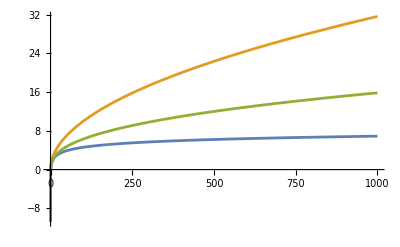

```mathematica
Plot[{Log[x],x^(1/2),x^(2/5)},{x,0,1000}]
```